```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

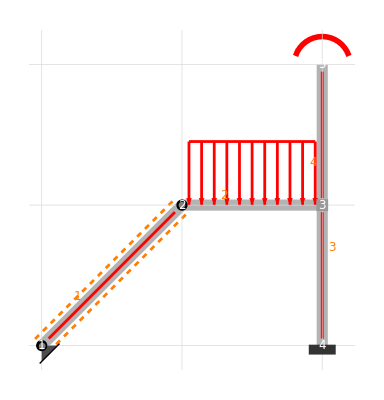

```mathematica
example={$$nodes->{{-L, -L}, {0, 0}, {L, 0}, {L, -L}, {L, L}},
$$edges->{{1, 2}, {2, 3}, {3, 4}, {3, 5}},$$absname->s,
$$constraints->{{{"hinge", 1}}, {{"hinge", 1, 2}}, {{"clamp", 2, 3}, {"clamp", 3, 4}}, {{"clamp", 3}}, {{"free", 4}}},
$$bodyloads->{{2, {0, -q, 0}}},
$$nodalloads->{{5, {0, 0, q L^2}}},
$$predeformations->{{1, {α ΔT, 0, 0}}},
$$cdisplacements->{{1, {0, 0, 0}}},
$$EIoverEAL2->0};
(*All constraints are initialized to hinge constraints; use "BFConstraintsPalette[BFConstraintTypes];" to input different constraints.*)
BFShowInput[example]
```

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
BFClassify[example]; sol = {{Ns, Qs, Ms}, details} = BFForcesSolve[example];
(*A=Transpose[First[BFStaticProblem[example]]];MatrixForm[A]
BFShowRigidMotions[example]*)
(*BFEquations[example,"Nodal"]; sol = {{us, vs}, {Ns, Qs, Ms}, details} = BFDisplacementsSolve[example];*)
gsol=BFShowOutput[example, sol]
```

BFClassify::su: Statically undetermined system of order 1.
13 possible choices of static unknows are as follows:
1
N_1[0] | 2
N_1[1] | 3
N_2[0] | 4
Q_2[0] | 5
N_2[1] | 6
Q_2[1] | 7
M_2[1] | 8
N_3[0] | 9
Q_3[0] | 10
M_3[0]
11
N_3[1] | 12
Q_3[1] | 13
M_3[1] |   |   |   |   |   |   |

BFClassify::kd: Kinematically determined system.

BFForcesSolve::suc: Chosen set of static unknows: {N_1[0]}

12345

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Dimensionless abscissa

s

Static equilibrium matrix

{{-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,√2 L,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,L,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,L,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,L,1},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-√2,√2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-√2,-√2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}}

Static equilibrium vector

{0,0,0,0,L q,(L^2 q)/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-L^2 q}

Fredholm condition: are the loads orthogonal to allowed rigid motions?

True

Bending stiffnesses

{EI,EI,EI,EI}

Axial stiffnesses

{∞,∞,∞,∞}

Degree of static undetermination

1

Some possible choices for the static unknowns

{{("N")_("1")[0]},{("N")_("1")[1]},{("N")_("2")[0]},{("Q")_("2")[0]},{("N")_("2")[1]},{("Q")_("2")[1]},{("M")_("2")[1]},{("N")_("3")[0]},{("Q")_("3")[0]},{("M")_("3")[0]},{("N")_("3")[1]},{("Q")_("3")[1]},{("M")_("3")[1]}}

Actually chosen static unknowns

{("N")_("1")[0]}

Reactions in the auxiliary problem 0

{{0,0,0,0,0,0},{0,0,0,0,L q,-(L^2 q)/2},{-L q,0,-(3 L^2 q)/2,-L q,0,-(3 L^2 q)/2},{0,0,L^2 q,0,0,L^2 q}}

Reactions in the auxiliary problem 1

{{1,0,0,1,0,0},{1/(√2),1/(√2),0,1/(√2),1/(√2),-L/(√2)},{-1/(√2),1/(√2),-L/(√2),-1/(√2),1/(√2),-√2 L},{0,0,0,0,0,0}}

Internal actions (N,Q,M) in the auxiliary problem 0

{{0,0,-L q,0},{0,L q s,0,0},{0,-1/2 L^2 q s^2,-(3 L^2 q)/2,L^2 q}}

Internal actions (N,Q,M) in the auxiliary problem 1

{{1,1/(√2),-1/(√2),0},{0,1/(√2),1/(√2),0},{0,-(L s)/(√2),-(L (1+s))/(√2),0}}

Mohr's Integrals: coefficient matrix ηij

{{(4 L^3)/(3 EI)}}

Mohr's Integrals: vector ηi0

{(19 L^4 q)/(8 √2 EI)+√2 L α ΔT}

Mohr's Integrals: solution for the static unknowns

{("N")_("1")[0]→-(3 (19 L^3 q+16 EI α ΔT))/(32 √2 L^2)}

Actual reactions

{{-(3 (19 L^3 q+16 EI α ΔT))/(32 √2 L^2),0,0,-(3 (19 L^3 q+16 EI α ΔT))/(32 √2 L^2),0,0},{-(57 L q)/64-(3 EI α ΔT)/(4 L^2),-(57 L q)/64-(3 EI α ΔT)/(4 L^2),0,-(57 L q)/64-(3 EI α ΔT)/(4 L^2),(7 L q)/64-(3 EI α ΔT)/(4 L^2),(25 L^2 q)/64+(3 EI α ΔT)/(4 L)},{-(7 L q)/64+(3 EI α ΔT)/(4 L^2),-(57 L q)/64-(3 EI α ΔT)/(4 L^2),-(39 L^2 q)/64+(3 EI α ΔT)/(4 L),-(7 L q)/64+(3 EI α ΔT)/(4 L^2),-(57 L q)/64-(3 EI α ΔT)/(4 L^2),(9 L^2 q)/32+(3 EI α ΔT)/(2 L)},{0,0,L^2 q,0,0,L^2 q}}

Actual internal actions (N,Q,M)

{{-(3 (19 L^3 q+16 EI α ΔT))/(32 √2 L^2),-(57 L q)/64-(3 EI α ΔT)/(4 L^2),-(7 L q)/64+(3 EI α ΔT)/(4 L^2),0},{0,L q (-57/64+s)-(3 EI α ΔT)/(4 L^2),-(57 L q)/64-(3 EI α ΔT)/(4 L^2),0},{0,(s (L^3 q (57-32 s)+48 EI α ΔT))/(64 L),3/64 L^2 q (-13+19 s)+(3 EI (1+s) α ΔT)/(4 L),L^2 q}}

-Graphics-

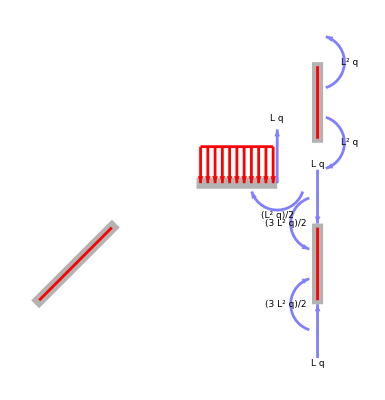

-Graphics-

-Graphics-

-Graphics-

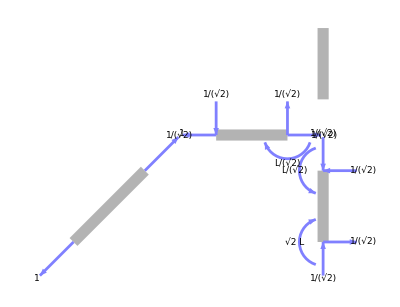

-Graphics-

-Graphics-

-Graphics-

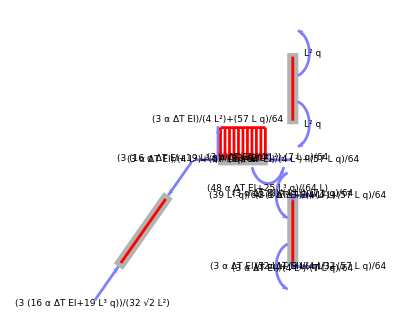

-Graphics-

-Graphics-

-Graphics-